## QuantumChannel Documentation

### Preamble

```mathematica
Needs["QuantumChannel`"]
```

The following packages are needed to run some code found in this documentation notebook.

```mathematica
Needs["QuantumSystems`"]
Needs["Visualization`"]
```

### Source Code

Open Source Code

## Introduction and Overview

QuantumChannel provides tools for storing, manipulating, and using quantum channels, as well as tools for converting between representations. Tests for properties such as complete positivity are included, and some common measures such as process fidelity. The dimensions of the input and output spaces do not necessarily have to match. Arbitrary bases can be used for basis dependent representations.

## Quantum Channels

### QuantumChannel

Quantum Channel Representation
QuantumChannel is the Head used to internally represent quantum channels. A valid quantum channel will be stored as
QuantumChannel[obj,{ChannelRep→rep,InputDim→dIn,OutputDim→dOut,Basis→basis}] 
where
• obj is the matrix or appropriate object of the channel in the current representation,
• rep is the label which specifies the representation of ‘obj’, valid representations are Unitary, Super, Choi, Chi, Kraus, Stinespring, SysEnv,
• dI is the dimension of the input Hilbert space of the channel,
• dOut is the dimension of the output Hilbert space of the channel,
• basis the the vectorization convention Basis used to represent the channel in the Choi and Super representations.

Quantum Channel Display Formatting
When displayed as output in the Mathematica GUI a QuantumChannel chan is displayed as: rep[obj,<params>].

Extracting Quantum Channel Data
• The physical matrix for the channel may be extracted by First[chan].
• The parameters may be extracted by ChannelParameters[chan] to return the list {ChannelRep→rep,InputDim→dIn,OutputDim→dOut,Basis→basis}, or by ChannelRep[chan], InputDim[chan], OutputDim[chan], Basis[chan]] to return individual parameters.

Changing Quantum Channel Representations
A QuantumChannel may have its representation transformed by: newRep[chan].

Quantum Channel Evolution
A QuantumChannel may be applied to a state to compute its evolution by chan[state]
where state is either a vector of dimension dIn, a square matrix of dimension {dIn,dIn}, or a vectorized square matrix of dimension {dIn*dIn,1} or {dIn*dIn}. If the input is a vectorized matrix, it is assumed to be vectorized in the Basis corresponding to chan.

Constructing Quantum Channels
The construction of quantum channel is achieved by applying the appropriate representation function to an operator.
Example: Unitary[U], Super[S],  Kraus[{K1,K2,...,Kn}].
Channels input this way will assume the default Vec Basis and attempt to automatically calculate the input and output dimensions. Input and output dimensions, and basis may be specified manually using options.
Example: Super[S,Basis→”Pauli”], or Choi[M, InputDim→4, OutputDim→2].

Quantum Channel Operations
The following operations may be applied to quantum channels
• Plus: multiple channels with the same input and output dimensions may be added or subtracted, this is done by converting the channels to the Super representation.
• Times:  channel may be multiplied by a scalar (numeric or symbolic). This applies to Unitary, Choi and Super representations. All other representations are first converted to the Super representation.
• Dot: multiple channels may be composed if the output dimension of one matches the input dimension of the following channel. This is done by converting the channels to the Super representation.
• Tr: may be applied to channels in the Unitary, Super, or Choi representations to compute the trace of the respective matrix. If applied to a channel that is not in one of these representations it will return an error.
• Transpose, ConjugateTranspose, Conjugate, MatrixExp, MatrixPower, MatrixLog: may be applied to a channel and the corresponding operation will be applied to the Super representation of the channel.
• KroneckerProduct, CircleTimes: multiple channels may be tensor producted together. This is done via the Choi matrix representation and automatically preserves the location of subsystems by applying the appropriate Reravel transformation.
• Eigenvalues, Eigenvectors, Eigensystem: Returns the Eigenvalues, Eigenvectors or Eigensystem for the Choi matrix representation of a QuantumChannel chan.

Quantum Channel Functions
The following operations may be applied to quantum channels
• MatrixForm, MatrixPlot, ArrayPlot: Display the matrix First[chan] according to the applied function.
• SparseArray, Normal, Simplify, FullSimplify, Refine, ComplexExpand, FunctionExpand, PowerExpand, ExpToTrig, TrigToExp, TrigExpand, TrigFactor, TrigReduce: Apply the function to the data stored in First[chan] of the QuantumChannel chan, including support for any optional arguments.

#### Options

Option | Default Value | Description
InputDim | Automatic | InputDim is the input dimension option for QuantumChannel. Additionally, InputDim[chan] returns the dimension of the input space of the QuantumChannel chan.
OutputDim | Automatic | OutputDim is the output dimension option for QuantumChannel. Additionally, OutputDim[chan] returns the dimension of the output space of the QuantumChannel chan.
Basis | Automatic | Basis is the option for QuantumChannel which specifies the representation basis; see Tensor`Basis. Additionally, Basis[chan] returns the vectorization basis for the QuantumChannel chan. This basis used for the Super and Choi representations of chan.

#### InputDim

InputDim is the input dimension option for QuantumChannel. Additionally, InputDim[chan] returns the dimension of the input space of the QuantumChannel chan.

#### OutputDim

OutputDim is the output dimension option for QuantumChannel. Additionally, OutputDim[chan] returns the dimension of the output space of the QuantumChannel chan.

#### Basis

Basis is the option for QuantumChannel which specifies the representation basis; see Tensor`Basis. Additionally, Basis[chan] returns the vectorization basis for the QuantumChannel chan. This basis used for the Super and Choi representations of chan.

Note that Basis is also defined in the Tensor` package.

### Unitary

Construction
Unitary[mat,opts] specifies that a matrix mat is a QuantumChannel and in the Unitary representation.

Transformation
Unitary[chan,opts] returns the QuantumChannel chan in its current representation while applying any specified options opts.

Options
• Basis→basis specifies the Vec Basis for transformations into the Super and Choi representations. The default Basis option is the default Vec Basis option.

Evolution
A QuantumChannel in Unitary representation may be applied to a state to compute its evolution. 
If chan = Unitary[U]:
• chan[vec] returns a vector formed from applying the unitary to the input vector or column vector vec
• chan[mat] returns the the square matrix output for apply chan to input square matrix mat.
• chan[vecMat] returns a vector formed from applying chan to the vectorized input matrix vecMat, where vecMat is a vector or column vector corresponding to a vectorized square matrix.

See QuantumChannel for further information.

#### Example

Constructing a unitary matrix for the Pauli-X gate

```mathematica
U1=Unitary[TP[X]]
```

Unitary[{{0,1},{1,0}},<params>]

Computing unitary evolution to an initial pure state:

```mathematica
U1[{α,β}]
```

{β,α}

Or a mixed state

```mathematica
U1[Array[a,{2,2}]]//MatrixForm
```

(a[2,2] | a[2,1]
a[1,2] | a[1,1])

### Super

Construction
Super[mat,opts] specifies that a matrix mat is a QuantumChannel and in the Super representation.

Transformation
Super[chan,opts] returns the QuantumChannel chan into the Super representation while applying any specified options opts.

Options
• Basis→basis specifies the Vec Basis of the input matrix, and specifies the Basis to transform into when transforming to the Super representation. The default Basis option is the default Vec Basis option.
Example: Basis→”Pauli” may be used to specify the input is a superoperator in the Pauli basis, or to transform a Super QuantumChannel into the Pauli basis.
See Basis for further information.

Evolution
A QuantumChannel in Super representation may be applied to a state to compute its evolution. 
If chan = Super[S]:
• chan[vec] returns the square matrix chan[Projector[vec]], for the input vector or column vector vec.
• chan[mat] returns the the square matrix output for apply chan to input square matrix mat.
• chan[vecMat] returns S.vecMat, where vecMat is a vector or column vector corresponding to a vectorized square matrix.

See QuantumChannel for further information.

#### Example

Convertign the previous unitary U1 into a superoperator

```mathematica
S1=Super[U1]
S1//MatrixForm
```

Super[{{0,0,0,1},{0,0,1,0},{0,1,0,0},{1,0,0,0}},<params>]

(0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0
1 | 0 | 0 | 0)

Computing unitary evolution to an initial pure state, note that now the output is a density matrix as in general superoperators may include dissipative evolution:

```mathematica
S1[{α,β}]//FullSimplify//MatrixForm
```

(Abs[β]^2 | β Conjugate[α]
α Conjugate[β] | Abs[α]^2)

The density matrix output is the same however, as it should be:

```mathematica
S1[Array[a,{2,2}]]//MatrixForm
```

(a[2,2] | a[2,1]
a[1,2] | a[1,1])

We may also convert this to a superoperator in the Pauli basis using:

```mathematica
Super[S1,Basis->"Pauli"]
%//MatrixForm
```

Super[{{1,0,0,0},{0,1,0,0},{0,0,-1,0},{0,0,0,-1}},<params>]

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

### Choi

Construction
Choi[mat,opts] specifies that a matrix mat is a QuantumChannel and in the Choi representation.

Transformation
Choi[chan,opts] returns the QuantumChannel chan into the Choi representation while applying any specified options opts.

Options
• InputDim→dIn   specifies the dimension of the input space. If this is not specified it will attempt to infer the output space for input matrix mat automatically. If this is fails it will return an error.
• OutputDim→dOut  specifies the dimension of the output space. If this is not specified it will attempt to infer the output space for input matrix mat automatically. If this is fails it will return an error.
• Basis→basis specifies the Vec Basis of the input matrix, and specifies the Basis to transform into when transforming to the Choi representation. The default Basis option is the default Vec Basis option.
Example: Basis→”Pauli” may be used to specify the input is a Choi matrix in the Pauli basis (aka a Chi matrix), or to transform a Choi QuantumChannel into the Pauli basis (into a Chi matrix).
See Basis for further information.

Evolution
A QuantumChannel in Choi representation may be applied to a state to compute its evolution. 
If chan = Choi[Λ]:
• chan[vec] returns the square matrix chan[Projector[vec]], for the input vector or column vector vec.
• chan[mat] returns the the square matrix output for apply chan to input square matrix mat.
• chan[vecMat] returns a vector formed from applying chan to the vectorized input matrix vecMat, where vecMat is a vector or column vector corresponding to a vectorized square matrix.

See QuantumChannel for further information.

#### Example 1

We may construct the Choi-matrix for the completely depolarizing channel from an identity matrix:

```mathematica
Λdp=Choi[IdentityMatrix[4]/2]
```

Choi[{{1/2,0,0,0},{0,1/2,0,0},{0,0,1/2,0},{0,0,0,1/2}},<params>]

To see this is the depolarizing channel, for an arbitrary initial operator A we have:

```mathematica
Λdp[Array[a,{2,2}]]//FullSimplify//MatrixForm
```

(1/2 (a[1,1]+a[2,2]) | 0
0 | 1/2 (a[1,1]+a[2,2]))

Which is Tr[A]*𝟙/2. Hence if Tr[A]=1 as for a density matrix we have that this is the maximally mixed state.

#### Example 2

To input a Chi-matrix as a Choi-matrix we may specify that the input is in the Pauli Basis. Consider a Pauli-Channel 
 ρ →1/2( p_0 ρ+p_1 XρX^†+p_2 YρY^†+p_3 ZρZ^†)

```mathematica
Λpauli=Choi[DiagonalMatrix[{p0,p1,p2,p3}],Basis->"Pauli"]
```

Choi[{{p0,0,0,0},{0,p1,0,0},{0,0,p2,0},{0,0,0,p3}},<params>]

```mathematica
Λpauli//Basis
```

Pauli

The output state is

```mathematica
Λpauli[Array[a,{2,2}]]//FullSimplify//MatrixForm
```

(1/2 ((p0+p3) a[1,1]+(p1+p2) a[2,2]) | 1/2 ((p0-p3) a[1,2]+(p1-p2) a[2,1])
1/2 ((p1-p2) a[1,2]+(p0-p3) a[2,1]) | 1/2 ((p1+p2) a[1,1]+(p0+p3) a[2,2]))

To convert to a Choi matrix in the standard Col basis we may run

```mathematica
Choi[Λpauli,Basis->"Col"]
```

Choi[{{p0/2+p3/2,0,0,p0/2-p3/2},{0,p1/2+p2/2,p1/2-p2/2,0},{0,p1/2-p2/2,p1/2+p2/2,0},{p0/2-p3/2,0,0,p0/2+p3/2}},<params>]

#### Example 3

For Choi-matrices with different input and output dimensions we need to specify thes dimensions. Consider, for example, a channel which acts as an identity channel on the input state, but adds an ancilla system initialized in the ground state to the system: ρ→ ρ⊗|0⟩⟨0|

The Choi-matrix for the identity Channel alone is:

```mathematica
Choi[Projector[Vec[IdentityMatrix[2]]]]
```

Choi[{{1,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,1}},<params>]

```mathematica
Choi[Projector[Vec[IdentityMatrix[2]]]][Array[a,{2,2}]]//MatrixForm
```

(a[1,1] | a[1,2]
a[2,1] | a[2,2])

For the full channel note that since the input and output dimensions are different we must specify one manually or we return an error:

```mathematica
Choi[Projector[Vec[IdentityMatrix[2]]]⊗Projector[{1,0}]]
```

QuantumChannel::dims: Input channel matrix needs specification of input and output dimensions.

The correct way to input this channel is one of the following:

```mathematica
Λ3=Choi[Projector[Vec[IdentityMatrix[2]]]⊗Projector[{1,0}],InputDim->2]
Λ3=Choi[Projector[Vec[IdentityMatrix[2]]]⊗Projector[{1,0}],OutputDim->4]
```

Choi[{{1,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0}},<params>]

Choi[{{1,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{1,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0}},<params>]

To see the evolution of this Channel:

```mathematica
Λ3[Array[a,{2,2}]]//MatrixForm
```

(a[1,1] | 0 | a[1,2] | 0
0 | 0 | 0 | 0
a[2,1] | 0 | a[2,2] | 0
0 | 0 | 0 | 0)

### Chi

Construction
Chi[mat,opts] specifies that a matrix mat is a QuantumChannel and in the Choi representation in the Pauli basis (unless another basis is specified as an option). The Choi matrix in different bases is also known as a Chi matrix.

Transformation
Chi[chan,opts] returns the QuantumChannel chan into the Choi representation in the Pauli basis if no basis is specified as an option. If a basis is specified it will transform to the Choi matrix in that basis.

Options
• InputDim→dIn   specifies the dimension of the input space. If this is not specified it will attempt to infer the output space for input matrix mat automatically. If this is fails it will return an error.
• OutputDim→dOut  specifies the dimension of the output space. If this is not specified it will attempt to infer the output space for input matrix mat automatically. If this is fails it will return an error.
• Basis→basis specifies the Vec Basis of the input matrix.  If this is not specified it defaults to Pauli basis. If this option is set Chi functions identically to Choi.
See Basis and Choi for further information.

Evolution
A QuantumChannel in Chi (Choi) representation may be applied to a state to compute its evolution. 
If chan = Chi[χ]:
• chan[vec] returns the square matrix chan[Projector[vec]], for the input vector or column vector vec.
• chan[mat] returns the the square matrix output for apply chan to input square matrix mat.
• chan[vecMat] returns a vector formed from applying chan to the vectorized input matrix vecMat, where vecMat is a vector or column vector corresponding to a vectorized square matrix.

See QuantumChannel for further information.

#### Example

Chi is really just shorthand for Choi[ _, Basis→”Pauli” ]

```mathematica
Chi[Array[χ,{4,4}]]
Choi[Array[χ,{4,4}],Basis->"Pauli"]
```

Choi[{{χ[1,1],χ[1,2],χ[1,3],χ[1,4]},{χ[2,1],χ[2,2],χ[2,3],χ[2,4]},{χ[3,1],χ[3,2],χ[3,3],χ[3,4]},{χ[4,1],χ[4,2],χ[4,3],χ[4,4]}},<params>]

Choi[{{χ[1,1],χ[1,2],χ[1,3],χ[1,4]},{χ[2,1],χ[2,2],χ[2,3],χ[2,4]},{χ[3,1],χ[3,2],χ[3,3],χ[3,4]},{χ[4,1],χ[4,2],χ[4,3],χ[4,4]}},<params>]

### Kraus

Construction
Kraus[{K1,...,Kn},opts] specifies that a list of matrices {K1,...,Kn} is a QuantumChannel and in the Kraus representation.
Kraus[{{K1,...,Kn},{L1,...,Ln}},opts] specifies that a list of matrices are a QuantumChannel and in the generalized Kraus representation.

Transformation
Kraus[chan,opts] returns the QuantumChannel chan into the Kraus representation while applying any specified options opts.

Options
• Basis→basis specifies the Vec Basis for transformations into the Super and Choi representations. The default Basis option is the default Vec Basis option.

Evolution
A QuantumChannel in Kraus representation may be applied to a state to compute its evolution. 
If chan = Kraus[{K1,...,Kn}]:
• chan[vec] returns the square matrix chan[Projector[vec]], for the input vector or column vector vec.
• chan[mat] returns the the square matrix output for apply chan to input square matrix mat.
• chan[vecMat] returns a vector formed from applying chan to the vectorized input matrix vecMat, where vecMat is a vector or column vector corresponding to a vectorized square matrix.

See QuantumChannel for further information.

#### Example

Inputing a Kraus map for a bit-flip error channel with error probability p.

```mathematica
chan=Kraus[{√(1-p)TP[I],√p TP[X]}]
```

Kraus[{{{√(1-p),0},{0,√(1-p)}},{{0,√p},{√p,0}}},<params>]

```mathematica
FullSimplify[chan[Array[a,{2,2}]],0≤p≤1]//MatrixForm
```

(-(-1+p) a[1,1]+p a[2,2] | -(-1+p) a[1,2]+p a[2,1]
p (a[1,2]-a[2,1])+a[2,1] | p (a[1,1]-a[2,2])+a[2,2])

### Stinespring

Construction
Stinespring[mat,opts] specifies that a matrix mat is a QuantumChannel and in the Stinespring representation.

Stinespring[{mat1,mat2},opts] specifies that the matrices {mat1,mat2} are a QuantumChannel and in the generalized Stinespring representation.

Transformation
Stinespring[chan,opts] returns the QuantumChannel chan into the Stinespring representation while applying any specified options opts.

Options
• OutputDim→dOut  specifies the dimension of the output space. If this is not specified it will attempt to infer the output space for input matrix mat automatically. If this is fails it will return an error.
• Basis→basis which specifies the Vec Basis for transformations into the Super and Choi representations. The default Basis option is the default Vec Basis option.

Evolution
A QuantumChannel in Stinespring representation may be applied to a state to compute its evolution. 
If chan = Stinespring[A]:
• chan[vec] returns the square matrix chan[Projector[vec]], for the input vector or column vector vec.
• chan[mat] returns the the square matrix output for apply chan to input square matrix mat.
• chan[vecMat] returns a vector formed from applying chan to the vectorized input matrix vecMat, where vecMat is a vector or column vector corresponding to a vectorized square matrix.

See QuantumChannel for further information.

#### Example

Converting the previous Kraus example to the Stinespring representation:

```mathematica
chan=Kraus[{√(1-p)TP[I],√p TP[X]}];
Stinespring[chan]
```

Stinespring[{{√(1-p),0},{0,√p},{0,√(1-p)},{√p,0}},<params>]

### System-Environment

Construction
SysEnv[{mat,vec},opts] specifies that the matrix mat and vector vec are a QuantumChannel and in the SysEnv representation.
SysEnv[{{mat1,mat2},vec},opts] specifies that the matrices {mat1,mat2} and vector vec are a QuantumChannel and in the generalized SysEnv representation.

Transformation
SysEnv[chan,opts] returns the QuantumChannel chan into the SysEnv representation while applying any specified options opts.

Options
• Basis→basis which specifies the Vec Basis for transformations into the Super and Choi representations. The default Basis option is the default Vec Basis option.

Evolution
A QuantumChannel in SysEnv representation may be applied to a state to compute its evolution. 
If chan = SysEnv[{U,v0}]:
• chan[vec] returns the square matrix chan[Projector[vec]], for the input vector or column vector vec.
• chan[mat] returns the the square matrix output for apply chan to input square matrix mat.
• chan[vecMat] returns a vector formed from applying chan to the vectorized input matrix vecMat, where vecMat is a vector or column vector corresponding to a vectorized square matrix.

See QuantumChannel for further information.

#### Example

```mathematica
chan=SysEnv[{TP[PM+MP],{e0,e1}}]
```

SysEnv[{{{0,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,0}},{e0,e1}},<params>]

```mathematica
chan[Array[a,{2,2}]]//MatrixForm
```

(e0 a[2,2] Conjugate[e0] | 0
0 | e1 a[1,1] Conjugate[e1])

### ChannelRep

ChannelRep[chan] returns the representation of the QuantumChannel chan.

#### Example

```mathematica
chan=Kraus[{TP[X],TP[Z]}];
ChannelRep[chan]
```

Kraus

```mathematica
ChannelRep[Super[chan]]
```

Super

### ChannelParameters

ChannelParameters[chan] returns the parameters of the QuantumChannel chan. This is a list of {ChannelRep→rep,InputDim→dIn,OutputDim→dOut,Basis→basis}.

#### Example

```mathematica
chan=Kraus[{Array[a,{2,2}],Array[b,{2,2}]}];
ChannelParameters[chan]
```

{ChannelRep→Kraus,InputDim→2,OutputDim→2,Basis→Col}

## Channel Predicates

### Completely Positive

CompletelyPositiveQ[chan] yeilds True if the QuantumChannel chan is a completely positive channel, and yields False otherwise.

CompletelyPositiveQ[chan,Simplify→fun] applies the pure function CompletelyPositiveQ[fun[choi]] where choi is the Choi matrix representaiton of chan. This may be used to simplify the expression with assumptions for symbolic channels.

Example: CompletelyPositiveQ[chan,FullSimplify[#,{a,b,c}∈Reals]&], or CompletelyPositiveQ[chan,ComplexExpand]

#### Example

This function only works for numeric channels

```mathematica
chan=Kraus[{√(1-1/4)TP[I],√(1/4)TP[X]}];
```

```mathematica
CompletelyPositiveQ[chan]
```

True

This fails to evaluate to a completely positive channel for a symbolic expression:

```mathematica
chan=Kraus[{√(1-p)TP[I],√p TP[X]}];
CompletelyPositiveQ[chan]
```

False

In this case we can check the eigenvalues of the Choi-matrix manually:

```mathematica
Simplify[Eigenvalues@chan,0≤p≤1]
```

{0,0,2-2 p,2 p}

### Trace Preserving

TracePreservingQ[chan] yeilds True if the QuantumChannel chan is a trace preserving channel, and yields False otherwise.

TracePreservingQ[chan,Simplify→fun] applies the pure function TracePreservingQ[fun[choi]] where choi is the Choi matrix representaiton of chan. This may be used to simplify the expression with assumptions for symbolic channels.

Example: TracePreservingQ[chan,FullSimplify[#,{a,b,c}∈Reals]&], or TracePreservingQ[chan,ComplexExpand]

### Hermitian Preserving

HermitianPreservingQ[chan] yeilds True if the QuantumChannel chan is a Hermitian preserving channel, and yields False otherwise.

HermitianPreservingQ[chan,Simplify→fun] applies the pure function HermitianPreservingQ[fun[choi]] where choi is the Choi matrix representaiton of chan. This may be used to simplify the expression with assumptions for symbolic channels.

Example: HermitianPreservingQ[chan,FullSimplify[#,{a,b,c}∈Reals]&], or HermitianPreservingQ[chan,ComplexExpand]

### Unital

UnitalQ[chan] yeilds True if the QuantumChannel chan is a unital channel, and yields False otherwise.

UnitalQ[chan,Simplify→fun] applies the pure function UnitalQ[fun[choi]] where choi is the Choi matrix representaiton of chan. This may be used to simplify the expression with assumptions for symbolic channels.

Example: UnitalQ[chan,FullSimplify[#,{a,b,c}∈Reals]&], or UnitalQ[chan,ComplexExpand]

#### Example

This test can fail for symbolic expressions if it doesnt explicitly evaluate to true. For example consider the Pauli Channel

```mathematica
chan=Chi[DiagonalMatrix[{p0,p1,p2,p3}]];
UnitalQ[chan]
```

False

However if we put in the assumptions that the diagonal terms sum to the dimension of the input space then it evaluates correctly:

```mathematica
UnitalQ[chan,Simplify->(FullSimplify[#,p0+p1+p2+p3==2]&)]
```

True

### Pauli Channel

PauliChannelQ[chan] yeilds True if the QuantumChannel chan is a Pauli channel, and yields False otherwise. A Pauli channel has a diagonal Choi-matrix when represented in the Pauli basis.

PauliChannelQ[chan,Simplify→fun] applies the pure function PauliChannelQ[fun[choi]] where choi is the Choi matrix representaiton of chan. This may be used to simplify the expression with assumptions for symbolic channels.

Example: PauliChannelQ[chan,FullSimplify[#,{a,b,c}∈Reals]&], or PauliChannelQ[chan,ComplexExpand]

#### Example

We check that a Pauli Channel is indeed a Pauli Channel:

```mathematica
chan=Chi[DiagonalMatrix[{p0,p1,p2,p3}]];
PauliChannelQ[chan]
```

True

## Channel Functions

### Process Fidelity

ProcessFidelity[chan] returns the process fidelity for comparing channel chan with the identity channel.

ProcessFidelity[chan1,chan2] returns the process fidelity for comparing chan1 to chan2.
The process fidelity of two channels with superoperators S1 and S2 is given by Tr[ConjugateTranspose[S1].S2].

#### Example

Compare the process fidelity of a bit-flip error channel to the identity channel:

```mathematica
chan=Kraus[{√(1-p)TP[I],√p TP[X]}];
ProcessFidelity[chan]//FullSimplify
```

Abs[1-p]

Compare the same channel to the bit-flip channel:

```mathematica
ProcessFidelity[chan,Unitary[TP[X]]]//FullSimplify
```

Abs[p]

### Gate Fidelity

GateFidelity[state,chan1,chan2] returns the gate fidelity Fidelity[chan2[state],chan1[state]]^2 for comparing the QuantumChannel chan1 to chan2 for the given input vector or density matrix state.

GateFidelity[state,chan] returns the gate fidelity for comparing chan to the identity channel.

#### Example

Checking for an X eigenstate, and a Z-eigenstate, and an arbitrary pure state.

```mathematica
chan=Kraus[{√(1-p)TP[I],√p TP[X]}];
```

```mathematica
FullSimplify[GateFidelity[{1,0},chan],0≤p≤1]
FullSimplify[GateFidelity[{1,1}/Sqrt[2],chan],0≤p≤1]
gfid=FullSimplify[GateFidelity[{α,β},chan],0≤p≤1&&Abs[α]^2+Abs[β]^2==1]
```

1-p

1

-(-1+p) Abs[α]^4-(-1+p) Abs[β]^4+p β^2 Conjugate[α]^2+2 α β Conjugate[α] Conjugate[β]+p α^2 Conjugate[β]^2

Check that the expression for the arbitrary state is consistant with the other values:

```mathematica
gfid/.{α->1,β->0}//FullSimplify
gfid/.{α->1/√2,β->1/√2}//FullSimplify
```

1-p

1

### Average Gate Fidelity

AverageGateFidelity[chan]returns the average gate fidelity for comparing the QuantumChannel chan to the identity channel averaged over all input states.

AverageGateFidelity[chan1,chan2] returns the average gate fidelity for comparing QuantumChannel chan1 to chan2  averaged over all input states. This is given by AverageGateFidelity[ConjugateTranspose[chan2].chan1].

#### Example

Computing the average gate fidelity of the bit-flip error channel:

```mathematica
chan=Kraus[{√(1-p)TP[I],√p TP[X]}];
FullSimplify[AverageGateFidelity[chan],0≤p≤1]
```

1-(2 p)/3

Comparing now to the bit-flip channel instead of the identity channel:

```mathematica
FullSimplify[AverageGateFidelity[chan,Unitary[TP[X]]],0≤p≤1]
```

1/3 (1+2 p)

### Entanglement Fidelity

EntanglementFidelity[state,chan] returns the  entanglement fidelity for comparing the  QuantumChannel chan1 to the identity channel for the given input state vector or density matrix state.

EntanglementFidelity[state,chan1,chan2] returns the entanglement fidelity for comparing QuantumChannel chan1 to chan2  for the given input vector or density matrix state. This is given by EntanglementFidelity[state,ConjugateTranspose[chan2].chan1].

#### Example 1

Checking for an X eigenstate, and a Z-eigenstate, and an arbitrary pure state. We see here that Entanglement Fidelity is equivalent to Gate Fidelity for pure states.

```mathematica
chan=Kraus[{√(1-p)TP[I],√p TP[X]}];
FullSimplify[EntanglementFidelity[{1,0},chan],0≤p≤1]
FullSimplify[EntanglementFidelity[{1,1}/Sqrt[2],chan],0≤p≤1]
efid=FullSimplify[EntanglementFidelity[{α,β},chan],0≤p≤1&&Abs[α]^2+Abs[β]^2==1]
```

1-p

1

-(-1+p) Abs[α]^4-(-1+p) Abs[β]^4+p β^2 Conjugate[α]^2+2 α β Conjugate[α] Conjugate[β]+p α^2 Conjugate[β]^2

#### Example 2

An example for mixed states shows that Entanglement Fidelity in general is different to GateFidelity:

```mathematica
chan=Kraus[{√(1-p)TP[I],√p TP[X]}];
efid=FullSimplify[EntanglementFidelity[{{3/4,0},{0,1/4}},chan],0≤p≤1]
gfid=Simplify[GateFidelity[{{3/4,0},{0,1/4}},chan],0≤p≤1]
```

1-p

1/16 (√(9-6 p)+√(1+2 p))^2

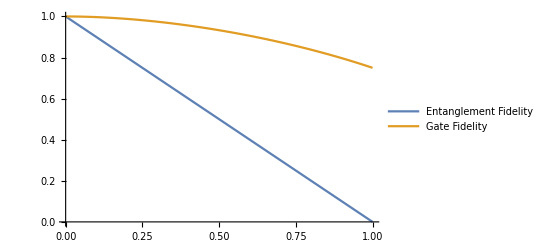

```mathematica
Plot[{efid,gfid},{p,0,1},PlotLegends->{"Entanglement Fidelity","Gate Fidelity"}]
```

### Channel Volume

ChannelVolume[chan] returns the volume of the hyperellipsoidal image of the Bloch-hypersphere under the action of a channel as a multiple of the unit hypersphere volume.

#### Example

```mathematica
chan=Kraus[{√(1-p)TP[I],√p TP[X]}];
FullSimplify[ChannelVolume[chan],0≤p≤1]
```

1-2 p

## Special Channels

### Commutator Channel

ComChannel[A] returns a QuantumChannel in the Super representation corresponding to the commutator superoperator Ad[A] defined by Ad[A][B]=A.B-B.A.
The input A must be a matrix or a Unitary QuantumChannel.

#### Example

This may be used to construct superoperators for Hamiltonian evolution according to the von-Neuman equation: dρ/dt=-i[H,ρ]

```mathematica
-I*ComChannel[TP[Z]]
```

Super[{{0,0,0,0},{0,2 ⅈ,0,0},{0,0,-2 ⅈ,0},{0,0,0,0}},<params>]

### Anti-Commutator Channel

ComChannel[A] returns a QuantumChannel in the Super representation corresponding to the anti-commutator superoperator AAd[A] defined by AAd[A][B]=A.B+B.A.
The input A must be a matrix or a Unitary QuantumChannel.

#### Example

This function is used for constructing the anti-commutator piece of a LindbladDissiaptor:

```mathematica
AComChannel[TP[P].TP[M]]
```

Super[{{2,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,0}},<params>]

To see this:

```mathematica
(Unitary[TP[M]]-1/2 AComChannel[TP[P].TP[M]])-LindbladDissipator[TP[M]]
```

Super[{{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}},<params>]

### Lindblad Dissipator Channel

LindbladDissipator[A] returns a QuantumChannel in the Super representation corresponding to the Lindblad dissipator D[A] defined by D[A][B]=A.B.A†-A†.A.B/2-B.A†.A/2.
The input A must be a matrix or a Unitary QuantumChannel.

LindbladDissipator[A1,...,An] returns LindbladDissipator[A1]+...+LindbladDissipator[An].

LindbladDissipator[{A1,...,An}] returns LindbladDissipator[A1]+...+LindbladDissipator[An].

#### Example 1

Construct the Lindblad dissipator for a T2 dephasing processs:

```mathematica
D1=1/(2T2)LindbladDissipator[TP[Z]]
```

Super[{{0,0,0,0},{0,-1/T2,0,0},{0,0,-1/T2,0},{0,0,0,0}},<params>]

To see the action of this dissipator

```mathematica
MatrixExp[t D1][Array[a,{2,2}]]//MatrixForm
```

(a[1,1] | ⅇ^(-t/T2) a[1,2]
ⅇ^(-t/T2) a[2,1] | a[2,2])

### Lindblad Equation Channel

Lindblad[mat] returns -I*ComChannel[mat], the Lindblad equation QuantumChannel for Hamiltonian evolution under mat.

Lindblad[{mat1,...,matn}] returns LindbladDissipator[mat1,...,matn], the Lindblad equation QuantumChannel for dissipative evolution with collapse operators mat1,...,matn.

Lindblad[expr1,expr2,...] evaluates each expression in the Sequence expr1,expr2,... as either a Hamiltonian or list of collapse operators and returns the QuantumChannel for the sum of the results.

#### Example

Consider a single spin-1/2 particle evolving under a T1 process:

```mathematica
spinSys=2π*Lindblad[ Spin[Z][1/2],{1/5 TP[M],1/10 TP[P]}];
states=With[{ΔS=MatrixExp[0.01 spinSys]},
NestList[ΔS,Projector[{1,1}/Sqrt[2]],1000]];
jz=Tr[#.Spin[Z][1/2]]&/@states;
jx=Tr[#.Spin[X][1/2]]&/@states;
```

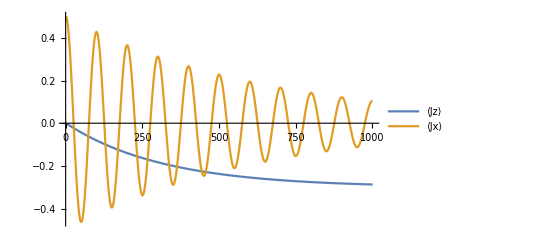

```mathematica
ListLinePlot[{jz,jx},PlotLegends->{"⟨Jz⟩","⟨Jx⟩"}]
```

### Partial Trace Channel

PartialTrChannel[{d1,d2,...,dn},{i1,...,ik}] returns a QuantumChannel in the Super representation corresponding to the partial trace: PartialTrChannel[{d1,d2,...,dn},{i1,...,ik}][B]=PartialTr[B,{d1,d2,...,dn},{i1,...,ik}].
• {d1,d2,...,dn} are the dimensions of the subsystem input Hilbert spaces.
• {i1,...,ik} is a list of the subsystems to be traced over.

#### Example

Partial Tr channel to trace out the second system of a bipartite system:

```mathematica
tr2=PartialTrChannel[{2,2},{1}]
```

Super[SparseArray[<8>, {4, 16}],<params>]

We can use this to construct an effective superoperator:

```mathematica
tr2.Unitary[TP[XX+YY]]
ChannelParameters[%]
```

Super[{{0,0,0,0,0,4,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,4,0,0,0,0,0}},<params>]

{ChannelRep→Super,InputDim→4,OutputDim→2,Basis→Col}

### FunctionChannel

FunctionChannel[fun,InputDim→dIn] returns a QuantumChannel in the Choi representation constructed using the Choi-Jamiolkowski isomorphism to apply the function fun to one half of a maximally entangled state on a dIn-dimensional input space. 
• fun may be any function that acts on {dIn,dIn} dimensional square matrices and returns a matrix or complex number. 

Options
• InputDim→dIn   specifies the dimension of the input space. If this is not specified it will result in an error.
• Basis→basis specifies the Vec Basis to convert the Choi matrix into. The default Basis option is “Col”.

#### Example

Construct the non-completely positive map corresponding to the Transpose operation on a 2-dimensional input space:

```mathematica
FunctionChannel[Transpose,InputDim->2]
%//MatrixForm
```

Choi[{{1,0,0,0},{0,0,1,0},{0,1,0,0},{0,0,0,1}},<params>]

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 1 | 0 | 0
0 | 0 | 0 | 1)